```mathematica
2-2
```

0

# Hexagonal Coordinate System

Nicholas Wheeler
20 January 2012

### Pre-introduction

While this work began as an attempt simply to discover an efficient way to coordinatize/identify/distinguish the nodes of a hexagonal grid, it proceeds to a sketch—made possible by that accomplishment—of the Markovian approach to random walks on such a grid. I am led to the conclusion that such an approach would require the resources of a supercomputer.

### Introduction

Here is the a portion of the unbounded hexagonal lattice on which, in recent work, I have constructed weighted random walks:

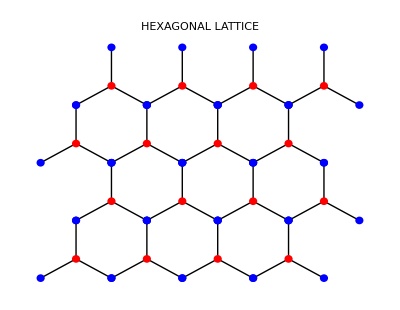

The nodes of the fundamental cell stand at noon, 2:00, 4:00, 6:00, 8:00 & 10:00 o'clock on the unit circle (center at the origin):

```mathematica
P[n_]:={Re[Exp[ⅈ(π/2-n π/3)]],Im[Exp[ⅈ(π/2-n π/3)]]}
```

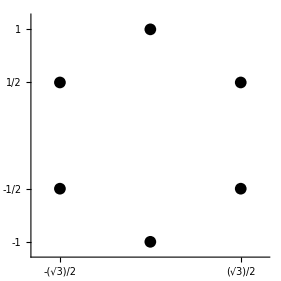

```mathematica
Graphics[{
{PointSize[0.03],Point[P[0]],Point[P[1]],Point[P[2]],Point[P[3]],Point[P[4]],Point[P[5]]}}, Axes->True, PlotRange->{{-1.1, 1.1},{-1.1, 1.1}}, Ticks->{{-(√3)/2,(√3)/2}, {-1,-1/2, 1/2,1}}]
```

My problem is to assign coordinates to nodes in such a way that (1) the coordinates of nearest-neighbor nodes are easily identified and (2) it becomes possible to associated nodes in a natural way with the elements of a Markov matrix and of the stochastic vectors on which those matrices act.

### Basic idea: red/blue nodal lines and their points of intersection

We observe that each red (ditto blue) node lies at the intersection points of a pair of sloping node rows. We undertake, therefore, to describe those linear rows.

Generally, the line on the (x, y)-plane that passes through the points (a_1,a_2) and  (b_1,b_2) is defined implicitly by the requirement that

```mathematica
Det[({{1, x, y}, {1, Subscript[a, 1], Subscript[a, 2]}, {1, Subscript[b, 1], Subscript[b, 2]}})]
```

-y a_1+x a_2+y b_1-a_2 b_1-x b_2+a_1 b_2

```mathematica
%==x(Subscript[a, 2]-Subscript[b, 2])-y(Subscript[a, 1]-Subscript[b, 1])+(Subscript[a, 1] Subscript[b, 2]-Subscript[a, 2] Subscript[b, 1])//Simplify
```

True

To obtain the lines that pass with positive/negative slope through the node at "noon" we construct

```mathematica
Det[({{1, x, y}, {1, 0, 1}, {1, -(√3)/2, -1/2}})]
Det[({{1, x, y}, {1, 0, 1}, {1, +(√3)/2, -1/2}})]
```

(√3)/2+(3 x)/2-(√3 y)/2

-(√3)/2+(3 x)/2+(√3 y)/2

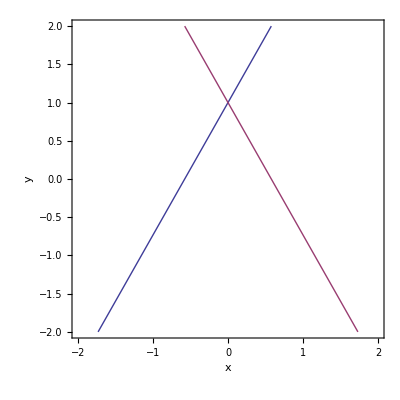

```mathematica
ContourPlot[{(√3)/2+(3 x)/2-(√3 y)/2==0,-(√3)/2+(3 x)/2+(√3 y)/2==0},{x,-2,2},{y,-2,2},Axes->True, AxesLabel->{x,y}]
```

We are interested in the x-translates of those lines, where the elemental translation carries

8 o'clock   ⟺   4 o'clock

and has length √3. We re led thus to define

```mathematica
Rup[x_, y_,n_]:=(√3)/2+(3 (x-n √3))/2-(√3 y)/2
Rdn[x_, y_,n_]:=-(√3)/2+(3 (x-n √3))/2+(√3 y)/2
```

where the function names suggest "Red up-slope" and "Red down-slope."

The red nodes of the fundamental hex-cell lie at three of the four points where these lines (two up-sloping, two down-sloping)

```mathematica
Join[Table[Rup[x,y,n]==0,{n,0,1}],Table[Rdn[x,y,m]==0,{m,-1,0}]]
```

{(√3)/2+(3 x)/2-(√3 y)/2==0,(√3)/2+3/2 (-√3+x)-(√3 y)/2==0,-(√3)/2+3/2 (√3+x)+(√3 y)/2==0,-(√3)/2+(3 x)/2+(√3 y)/2==0}

intersect. We plot those lines

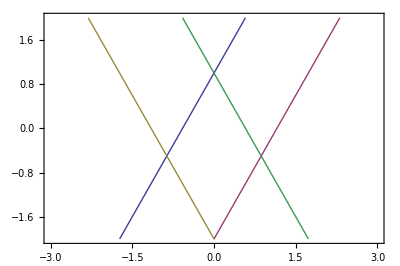

```mathematica
BasicRedLines=ContourPlot[{(√3)/2+(3 x)/2-(√3 y)/2==0,(√3)/2+3/2 (-√3+x)-(√3 y)/2==0,-(√3)/2+3/2 (√3+x)+(√3 y)/2==0,-(√3)/2+(3 x)/2+(√3 y)/2==0},{x,-3,3},{y,-2,2}, AspectRatio->Automatic,Axes->True]
```

The "noon," "4 o'clock" and "8 o'clock" nodes have coordinates given respectively by

```mathematica
{x,y}/.Solve[{Rup[x, y,0]==0,Rdn[x, y,0]==0},{x,y}]⟦1⟧
```

{0,1}

```mathematica
{x,y}/.Solve[{Rup[x, y,1]==0,Rdn[x, y,0]==0},{x,y}]⟦1⟧
```

{(√3)/2,-1/2}

```mathematica
{x,y}/.Solve[{Rup[x, y,0]==0,Rdn[x, y,-1]==0},{x,y}]⟦1⟧
```

{-(√3)/2,-1/2}

which we superimpose upon the preceding figure:

```mathematica
BasicRedNodes=Graphics[{Red,PointSize[0.03],Point[{{0,1},{(√3)/2,-1/2},{-(√3)/2,-1/2}}]}];
```

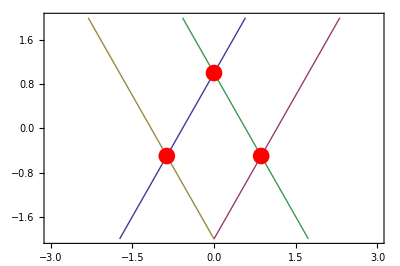

```mathematica
Show[{BasicRedLines, BasicRedNodes},Axes->True]
```

The down/up-sloping blue-node lines are got from the up/down-sloping red-node lines by this simple adjustment (reflection in the x-axis):

```mathematica
y⟶-y
```

Whence the constructions

```mathematica
Bdn[x_, y_,n_]:=(√3)/2+(3 (x-n √3))/2+(√3 y)/2
Bup[x_, y_,n_]:=-(√3)/2+(3 (x-n √3))/2-(√3 y)/2
```

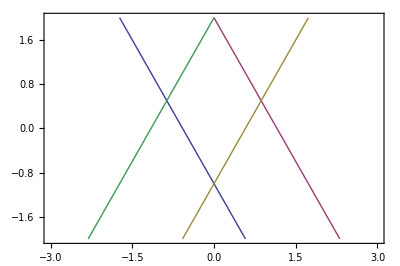

```mathematica
BasicBlueLines=ContourPlot[{Bdn[x,y,0]==0,Bdn[x,y,1]==0,
Bup[x,y,0]==0,Bup[x,y,-1]==0},{x,-3,3},{y,-2,2}, AspectRatio->Automatic,Axes->True]
```

```mathematica
{x,y}/.Solve[{Bup[x, y,0]==0,Bdn[x, y,0]==0},{x,y}]⟦1⟧
```

{0,-1}

```mathematica
{x,y}/.Solve[{Bup[x, y,0]==0,Bdn[x, y,1]==0},{x,y}]⟦1⟧
```

{(√3)/2,1/2}

```mathematica
{x,y}/.Solve[{Bup[x, y,-1]==0,Bdn[x, y,0]==0},{x,y}]⟦1⟧
```

{-(√3)/2,1/2}

```mathematica
BasicBlueNodes=Graphics[{Blue,PointSize[0.03],Point[{{0,-1},{(√3)/2,1/2},{-(√3)/2,1/2}}]}];
```

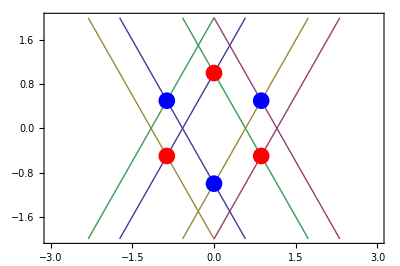

```mathematica
Show[{BasicRedLines, BasicBlueLines, BasicRedNodes, BasicBlueNodes}]
```

We have actually no interest in the red/blue nodal lines themselves (which were introduced only as a coordinating device), but only in their points of intersection. Accordingly,  we use

```mathematica
{x,y}/.Solve[{Rup[x, y,m]==0,Rdn[x, y,-n]==0},{x,y}]⟦1⟧
```

{1/2 (√3 m-√3 n),-(-2 √3+3 √3 m+3 √3 n)/(2 √3)}

to construct an {m.n}-indexed array of points (red nodes)

```mathematica
PR[m_,n_]:={(√3)/2 ( m- n),1-3/2 ( m+ n)}
```

```mathematica
Simplify[PR[m,n]=={(√3)/2 ( m- n),1-3/2 ( m+ n)}]
```

True

of which we plot a sample:

```mathematica
RedPopulation=Flatten[Table[PR[m,n],{m,-5,5},{n,-5,5}],1];
```

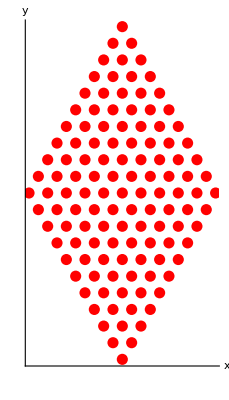

```mathematica
RedPopFig=Graphics[{Red, PointSize[0.02],Point[RedPopulation]}, Axes->True, AxesLabel->{x,y}, Ticks->False]
```

Similarly,

```mathematica
{x,y}/.Solve[{Bup[x, y,m]==0,Bdn[x, y,-n]==0},{x,y}]⟦1⟧
```

{1/2 (√3 m-√3 n),-(2 √3+3 √3 m+3 √3 n)/(2 √3)}

```mathematica
PB[m_,n_]:={(√3)/2 ( m- n),-1-3/2 ( m+ n)}
```

```mathematica
Simplify[PB[m,n]=={1/2 (√3 m-√3 n),-(2 √3+3 √3 m+3 √3 n)/(2 √3)}]
```

True

```mathematica
BluePopulation=Flatten[Table[PB[m,n],{m,-5,5},{n,-5,5}],1];
```

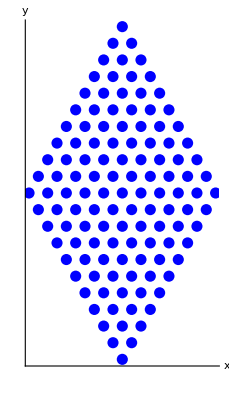

```mathematica
BluePopFig=Graphics[{Blue, PointSize[0.02],Point[BluePopulation]}, Axes->True, AxesLabel->{x,y}, Ticks->False]
```

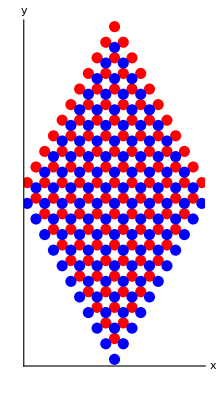

```mathematica
Show[{RedPopFig, BluePopFig}]
```

In construcing the red (ditto blue) nodes in this display we let m and n range independently on

{-5, -4, -3, -2, -1, 0, 1, 2, 3, 4, 5}

so there are 11^2= 121 red nodes, an equal number of blue nodes, and 242 nodes in total. 

If those nodes were connected—each to its to nearest neighbors to construct complete or (at the edges) partial hexagons—the top red and bottom blue nodes would become disconnected, leaving a connected graph with 240 nodes. Markov matrices that act on 240-dimensional stochastic vectors have 240^2= 57,600 elements. Since each node is connected to (at most) three others, such matrices would be "sparce," so computational management may not be out of the question.

### Nearest neighbors

Which three of the blue nodes PB[p, q] are nearest neighbors  of the red node PR[m, n]? 
Which three of the red nodes PR[p, q] are nearest neighbors  of the blue node PB[m, n]? 

In previous work I gave names as indicated in the following figure

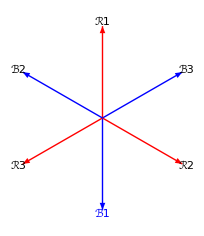

to the displacement vectors

```mathematica
R1={Cos[π/2],Sin[π/2]};
R2={Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]};
R3={Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]};
```

that proceed ● ⟶ ●, and

```mathematica
B1=-R1;
B2=-R2;
B3=-R3;
```

to  those that proceed ● ⟶ ● :

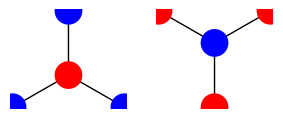

Specifically,

```mathematica
R1
R2
R3
```

{0,1}

{(√3)/2,-1/2}

{-(√3)/2,-1/2}

and

```mathematica
B1
B2
B3
```

{0,-1}

{-(√3)/2,1/2}

{(√3)/2,1/2}

A little experimentation  establishes that those vectors can be described

```mathematica
R1==Simplify[PB[m-1,n-1]-PR[m,n]]
R2==Simplify[PB[m ,n-1]-PR[m,n]]
R3==Simplify[PB[m -1,n]-PR[m,n]]

B1==Simplify[PR[m+1,n+1]-PB[m,n]]
B2==Simplify[PR[m ,n+1]-PB[m,n]]
B3==Simplify[PR[m +1,n]-PB[m,n]]
```

True

True

True

«3 more identical outputs»

Here are diagramatic representations of those results:

```mathematica
{{•, •, •, •}, {•, R1, R3, •}, {•, R2, PR[m,n], •}, {•, •, •, •}}
```

```mathematica
{{•, •, •, •}, {•, PB[m,n], B2, •}, {•, B3, B1, •}, {•, •, •, •}}
```

### Placing hexagonal node coordinates in linear array

This is the critical first step toward construction of the stochastic vectors and Markov matrices that enter into description of the averaged properties of random walks on hexagonal graphs.

To avoid the extraneous complications that arise when the {m, n}-indices are allowed to assume negative values I will assume that {m, n} ranges on the upper right quadrant of the unit lattice. Suppose, for example, that m and n range on {1, 2, 3, ... , 9}. We confront then the following hexagonal array of 162 nodes:

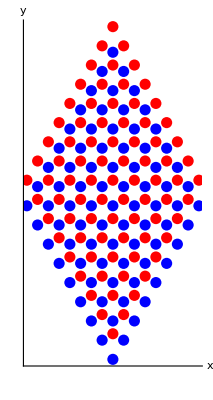

```mathematica
RedPopulation2=Flatten[Table[PR[m,n],{m,1,9},{n,1,9}],1];
RedPopFig2=Graphics[{Red, PointSize[0.02],Point[RedPopulation2]}, Axes->True, AxesLabel->{x,y}, Ticks->False, AxesOrigin->{0,0}];
BluePopulation2=Flatten[Table[PB[m,n],{m,1,9},{n,1,9}],1];
BluePopFig2=Graphics[{Blue, PointSize[0.02],Point[BluePopulation2]}, Axes->True, AxesLabel->{x,y}, Ticks->False, AxesOrigin->{0,0}];
Show[{RedPopFig2,BluePopFig2}]
```

```mathematica
Length[RedPopulation2]
Length[BluePopulation2]
```

81

81

To display the elements of the d × d matrix

(a_(1,1) | a_(1,2) | ⋯ | a_(1,d)
a_(2,1) | a_(2,2) | ⋯ | a_(2,d)
⋮ | ⋮ | ⋱ | ⋮
a_(d,1) | a_(d,2) | ⋯ | a_(d,d))

as a d^2-dimensional column vector I will (since I can think of no more sophisticated/natural procedure) simply stack column upon column, in dictionary order:

(e_1
e_2
⋮
e_d
e_(1+d)
e_(2+d)
⋮
e_(2d)
e_(1+2d)
e_(2+2d)
⋮
e_(3d)
•
•
•
•
e_(1-d+d^2)
e_(2-d+d^2)
⋮
e_(d^2))=(a_(1,1)
a_(1,2)
⋮
a_(1,d)
a_(2,1)
a_(2,2)
⋮
a_(2,d)
a_(3,1)
a_(3,2)
⋮
a_(3,d)
•
•
•
•
a_(d,1)
a_(d,2)
⋮
a_(d,d))

Generally

e_𝒥[m,n]=a_(m,n)

where

```mathematica
𝒥[m_,n_]:=d(m-1)+n
```

as I verify:

```mathematica
𝒥[1,1]//Expand
𝒥[1,2]//Expand
𝒥[1,d]//Expand
𝒥[2,1]//Expand
𝒥[2,2]//Expand
𝒥[2,d]//Expand
𝒥[3,1]//Expand
𝒥[3,2]//Expand
𝒥[3,d]//Expand
𝒥[d,1]//Expand
𝒥[d,2]//Expand
𝒥[d,d]//Expand
```

1

2

d

1+d

2+d

2 d

1+2 d

2+2 d

3 d

1-d+d^2

2-d+d^2

d^2

```mathematica
Table[Subscript[a, m,n],{m,1,9},{n,1,9}]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5) | a_(1,6) | a_(1,7) | a_(1,8) | a_(1,9)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5) | a_(2,6) | a_(2,7) | a_(2,8) | a_(2,9)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5) | a_(3,6) | a_(3,7) | a_(3,8) | a_(3,9)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5) | a_(4,6) | a_(4,7) | a_(4,8) | a_(4,9)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5) | a_(5,6) | a_(5,7) | a_(5,8) | a_(5,9)
a_(6,1) | a_(6,2) | a_(6,3) | a_(6,4) | a_(6,5) | a_(6,6) | a_(6,7) | a_(6,8) | a_(6,9)
a_(7,1) | a_(7,2) | a_(7,3) | a_(7,4) | a_(7,5) | a_(7,6) | a_(7,7) | a_(7,8) | a_(7,9)
a_(8,1) | a_(8,2) | a_(8,3) | a_(8,4) | a_(8,5) | a_(8,6) | a_(8,7) | a_(8,8) | a_(8,9)
a_(9,1) | a_(9,2) | a_(9,3) | a_(9,4) | a_(9,5) | a_(9,6) | a_(9,7) | a_(9,8) | a_(9,9))

To demonstrate (in this illustrative context) the success of

a_(m,n) ⟶ e_𝒥[m,n]

I assign to d the following value

```mathematica
d=9;
```

and obtain

```mathematica
Flatten[Table[Subscript[e, 𝒥[m,n]],{m,1,9},{n,1,9}],1]
```

{e_1,e_2,e_3,e_4,e_5,e_6,e_7,e_8,e_9,e_10,e_11,e_12,e_13,e_14,e_15,e_16,e_17,e_18,e_19,e_20,e_21,e_22,e_23,e_24,e_25,e_26,e_27,e_28,e_29,e_30,e_31,e_32,e_33,e_34,e_35,e_36,e_37,e_38,e_39,e_40,e_41,e_42,e_43,e_44,e_45,e_46,e_47,e_48,e_49,e_50,e_51,e_52,e_53,e_54,e_55,e_56,e_57,e_58,e_59,e_60,e_61,e_62,e_63,e_64,e_65,e_66,e_67,e_68,e_69,e_70,e_71,e_72,e_73,e_74,e_75,e_76,e_77,e_78,e_79,e_80,e_81}

To proceed in the reverse direction

```mathematica
Subscript[e, 𝒥] ⟶ Subscript[a, m[𝒥],n[𝒥]]
```

I use these number-theoretic commands

```mathematica
?Floor
```

Floor[x] gives the greatest integer less than or equal to x. 
Floor[x,a] gives the greatest multiple of a less than or equal to x.

```mathematica
?Mod
```

Mod[m,n] gives the remainder on division of m by n. 
Mod[m,n,d] uses an offset d.

to (after a little experimentation) construct

```mathematica
m[x_]:=Floor[(x-1)/d]+1
n[x_]:=Which[Mod[x,d]≠0,Mod[x,d],Mod[x,d]==0,9]
```

Here follow series of tests

```mathematica
Table[m[k],{k,1,9}]
Table[n[k],{k,1,9}]
```

{1,1,1,1,1,1,1,1,1}

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[m[k],{k,10,18}]
Table[n[k],{k,10,18}]
```

{2,2,2,2,2,2,2,2,2}

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[m[k],{k,5d+1,6d}]
Table[n[k],{k,5d+1,6d}]
```

{6,6,6,6,6,6,6,6,6}

{1,2,3,4,5,6,7,8,9}

```mathematica
𝒥[RandomInteger[{1,9}],RandomInteger[{1,9}]]
```

48

```mathematica
m[48]
n[48]
```

6

3

```mathematica
𝒥[6,3]
```

48

culminating in this grand demonstration:

```mathematica
Table[Subscript[a, m[j],n[j]],{j,1,d^2}]
```

{a_(1,1),a_(1,2),a_(1,3),a_(1,4),a_(1,5),a_(1,6),a_(1,7),a_(1,8),a_(1,9),a_(2,1),a_(2,2),a_(2,3),a_(2,4),a_(2,5),a_(2,6),a_(2,7),a_(2,8),a_(2,9),a_(3,1),a_(3,2),a_(3,3),a_(3,4),a_(3,5),a_(3,6),a_(3,7),a_(3,8),a_(3,9),a_(4,1),a_(4,2),a_(4,3),a_(4,4),a_(4,5),a_(4,6),a_(4,7),a_(4,8),a_(4,9),a_(5,1),a_(5,2),a_(5,3),a_(5,4),a_(5,5),a_(5,6),a_(5,7),a_(5,8),a_(5,9),a_(6,1),a_(6,2),a_(6,3),a_(6,4),a_(6,5),a_(6,6),a_(6,7),a_(6,8),a_(6,9),a_(7,1),a_(7,2),a_(7,3),a_(7,4),a_(7,5),a_(7,6),a_(7,7),a_(7,8),a_(7,9),a_(8,1),a_(8,2),a_(8,3),a_(8,4),a_(8,5),a_(8,6),a_(8,7),a_(8,8),a_(8,9),a_(9,1),a_(9,2),a_(9,3),a_(9,4),a_(9,5),a_(9,6),a_(9,7),a_(9,8),a_(9,9)}

The hexagonal array

-Graphics-

presents a duplex set of doubly-indexed nodal points:

{m,n}_red ⊕ {m,n}_blue

(a_(1,1) | a_(1,2) | ⋯ | a_(1,d)
a_(2,1) | a_(2,2) | ⋯ | a_(2,d)
⋮ | ⋮ | ⋱ | ⋮
a_(d,1) | a_(d,2) | ⋯ | a_(d,d))⊕(b_(1,1) | b_(1,2) | ⋯ | b_(1,d)
b_(2,1) | b_(2,2) | ⋯ | b_(2,d)
⋮ | ⋮ | ⋱ | ⋮
b_(d,1) | b_(d,2) | ⋯ | b_(d,d))

When those d^2+d^2 elements are deployed in columnar array we end up (in the case d = 9) with 162-dimensional column vectors that are to be multiplied by 162 ×162 Markov matrices that have (even though d = 9 constructs a very small sheet of graphene) already this very large number of elements:

```mathematica
(2×9^2)^2
```

26244

I elect to deploy those 2 d^2 in a columnar array of this design:

(e_1
⋮
e_(d^2)
e_(d^2+1)
⋮
e^(2 d^2))=(a_(1,1)
⋮
a_(d,d)
b_(1,1)
⋮
b_(d,d))

We now have

e_𝒥[m,n]=a_(m,n)
e_(d^2+𝒥[m,n])=b_(m,n)

where as before

𝒥[m_,n_]:=d(m-1)+n

It becomes natural at this point to modify that definition:

```mathematica
𝒥a[m_,n_]:=d(m-1)+n
𝒥b[m_,n_]:=d^2+d(m-1)+n
```

```mathematica
𝒥a[1,1]
𝒥a[9,9]
𝒥b[1,1]
𝒥b[9,9]
```

1

81

82

162

```mathematica
m[x_]:=Floor[(x-1)/d]+1
n[x_]:=Which[Mod[x,d]≠0,Mod[x,d],Mod[x,d]==0,9]
```

```mathematica
e[j_]:=Which[j≤d^2,Subscript[a, m[j],n[j]],j>d^2,Subscript[b, m[j-d^2],n[j-d^2]]]
```

```mathematica
Table[e[k],{k,1,18}]
```

{a_(1,1),a_(1,2),a_(1,3),a_(1,4),a_(1,5),a_(1,6),a_(1,7),a_(1,8),a_(1,9),a_(2,1),a_(2,2),a_(2,3),a_(2,4),a_(2,5),a_(2,6),a_(2,7),a_(2,8),a_(2,9)}

```mathematica
Table[e[k],{k,72,90}]
```

{a_(8,9),a_(9,1),a_(9,2),a_(9,3),a_(9,4),a_(9,5),a_(9,6),a_(9,7),a_(9,8),a_(9,9),b_(1,1),b_(1,2),b_(1,3),b_(1,4),b_(1,5),b_(1,6),b_(1,7),b_(1,8),b_(1,9)}

```mathematica
Table[e[k],{k,145,162}]
```

{b_(8,1),b_(8,2),b_(8,3),b_(8,4),b_(8,5),b_(8,6),b_(8,7),b_(8,8),b_(8,9),b_(9,1),b_(9,2),b_(9,3),b_(9,4),b_(9,5),b_(9,6),b_(9,7),b_(9,8),b_(9,9)}

### Structure of the adjacency matrix

Since stochastic vectors have the structure

e=(E
E)

and on a honeycomb no node is connected to a node of the same color, the adjacency matrix will have the form

𝔸=(𝕆 | 𝕊
𝕊^T | 𝕆)

where 𝕆 is the d^2×d^2 zero matrix and 𝕊 is a sparce d^2×d^2 matrix with 3 (but occasionally only 2) 1s on each row and all other elements 0. Which means that about

(d^2-3)/d^2 100%

of the elements in 𝕊 are 0s. In the case d = 9 this means that about 96% of the elements in 𝕊 are 0s. The following table shows how that % increases as the value of d ascends:

```mathematica
Table[{d,N[100 (d^2-3)/d^2]},{d,10,100,10}]//TableForm
```

10 | 97.
20 | 99.25
30 | 99.6667
40 | 99.8125
50 | 99.88
60 | 99.9167
70 | 99.9388
80 | 99.9531
90 | 99.963
100 | 99.97

We have discovered that the blue nearest neighbors of the red node

```mathematica
Subscript[{m,n}, red]
```

lie at

```mathematica
Subscript[{m-1,n-1}, blue], Subscript[{m,n-1}, blue], Subscript[{m-1,n}, blue]
```

we want to express this in terms of the 𝒥 coordinates that range on {1,... ,2 d^2}.

```mathematica
Clear[d]
𝒥a[m,n]
𝒥b[m,n]
```

d (-1+m)+n

d^2+d (-1+m)+n

From

```mathematica
𝒥b[m-1,n-1]-𝒥a[m,n]//Expand
𝒥b[m,n-1]-𝒥a[m,n]//Expand
𝒥b[m-1,n]-𝒥a[m,n]//Expand
```

-1-d+d^2

-1+d^2

-d+d^2

we obtain

```mathematica
𝒥a[m,n]-1-d+d^2==𝒥b[m-1,n-1]//Simplify
𝒥a[m,n]-1+d^2==𝒥b[m,n-1]//Simplify
𝒥a[m,n]-d+d^2==𝒥b[m-1,n]//Simplify
```

True

True

True

As m and n range on {1, 2, ... , 9} we see that

𝒥a[m,n]
𝒥b[m,n]

run though the expected values

```mathematica
d=9;
```

```mathematica
Table[𝒥a[m,n],{m,1,9},{n,1,9}]//MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27
28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36
37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45
46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54
55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63
64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72
73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81)

```mathematica
Table[𝒥b[m,n],{m,1,9},{n,1,9}]//MatrixForm
```

(82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99
100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108
109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117
118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126
127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135
136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144
145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153
154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162)

but that some of 𝒥-coordinates of the expected blue nearest neighbors of red nodes

𝒥b[m-1,n-1]
𝒥b[m,n-1]
𝒥b[m-1,n]

lie outside the accepted range {82 ≤ 𝒥 ≤ 162}, as I demonstrate by means of a single example:

```mathematica
Table[𝒥b[m-1,n-1],{m,1,9},{n,1,9}]//MatrixForm
```

(72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80
81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89
90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98
99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107
108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116
117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125
126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134
135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143
144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152)

I find by experimentation that to expunge those terms we must arrange for

m-1
n-1

never to assume negative values. That done, we get

```mathematica
Table[𝒥b[m-1,n-1],{m,2,9},{n,2,9}]//MatrixForm
```

(82 | 83 | 84 | 85 | 86 | 87 | 88 | 89
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98
100 | 101 | 102 | 103 | 104 | 105 | 106 | 107
109 | 110 | 111 | 112 | 113 | 114 | 115 | 116
118 | 119 | 120 | 121 | 122 | 123 | 124 | 125
127 | 128 | 129 | 130 | 131 | 132 | 133 | 134
136 | 137 | 138 | 139 | 140 | 141 | 142 | 143
145 | 146 | 147 | 148 | 149 | 150 | 151 | 152)

```mathematica
Table[𝒥b[m,n-1],{m,1,9},{n,2,9}]//MatrixForm
```

(82 | 83 | 84 | 85 | 86 | 87 | 88 | 89
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98
100 | 101 | 102 | 103 | 104 | 105 | 106 | 107
109 | 110 | 111 | 112 | 113 | 114 | 115 | 116
118 | 119 | 120 | 121 | 122 | 123 | 124 | 125
127 | 128 | 129 | 130 | 131 | 132 | 133 | 134
136 | 137 | 138 | 139 | 140 | 141 | 142 | 143
145 | 146 | 147 | 148 | 149 | 150 | 151 | 152
154 | 155 | 156 | 157 | 158 | 159 | 160 | 161)

```mathematica
Table[𝒥b[m-1,n],{m,2,9},{n,1,9}]//MatrixForm
```

(82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90
91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99
100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108
109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117
118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126
127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135
136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144
145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153)

To accomplish that snipping in 𝒥-language I introduce a snip factor constructed from

```mathematica
?UnitStep
```

UnitStep[x] represents the unit step function, equal to 0 for x<0 and 1 for x≥0. 
UnitStep[x_1,x_2,…] represents the multidimensional unit step function which is 1 only if none of the x_i are negative.

I proceed from

```mathematica
Clear[d]
```

```mathematica
𝒥b[m-1,n-1]==𝒥a[m,n]-1-d+d^2//Simplify
𝒥b[m,n-1]==𝒥a[m,n]-1+d^2//Simplify
𝒥b[m-1,n]==𝒥a[m,n]-d+d^2//Simplify
```

True

True

True

to the definitions

```mathematica
Subscript[J, 1][x_]:=x-1-d+d^2
Subscript[J, 2][x_]:=x-1+d^2
Subscript[J, 3][x_]:=x-d+d^2
```

Introducing the abbreviation

```mathematica
δ[x_,y_]:=KroneckerDelta[x,y]
```

we reinstate our illustrative d-value

```mathematica
d=9;
```

and to construct the 𝒥^th row of the adjacency matrix 𝔸 command

Table[UnitStep[j-83](δ[j,J_1[𝒥]]+δ[j,J_2[𝒥]]+δ[j,J_3[𝒥]]),{j,1,162}]

The 13^th row, for example, becomes

```mathematica
𝒥=13;Table[UnitStep[j-82](δ[j,Subscript[J, 1][𝒥]]+δ[j,Subscript[J, 2][𝒥]]+δ[j,Subscript[J, 3][𝒥]]),{j,1,162}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

in which

```mathematica
Total[%]
```

3

elements are 1, the other 159 are 0. Looking to the 81 × 81-dimensional 𝕊-matrix (within which all the 1s reside), we find the number of 1s in successive rows to be given by

```mathematica
Table[Total[Table[UnitStep[j-82](δ[j,Subscript[J, 1][𝒥]]+δ[j,Subscript[J, 2][𝒥]]+δ[j,Subscript[J, 3][𝒥]]),{j,82,162}]],{𝒥,1,81}]
```

{0,1,1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Length[%]
```

81

```mathematica
𝕊=Table[Table[UnitStep[j-82](δ[j,Subscript[J, 1][𝒥]]+δ[j,Subscript[J, 2][𝒥]]+δ[j,Subscript[J, 3][𝒥]]),{j,82,162}],{𝒥,1,81}];
```

```mathematica
Table[Total[𝕊⟦𝒥⟧],{𝒥,1,81}]
```

{0,1,1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
Det[𝕊]
```

0

The idea now is to construct

```mathematica
𝔸=({{𝕆, 𝕊}, {𝕋, 𝕆}})
```

where 𝕆 is the 81-dimensional zero matrix and 𝕋 denotes the transpose of 𝕊. To that end, I construct

```mathematica
ℤ=Table[0,{k,1,81}];
𝕆=DiagonalMatrix[ℤ];

𝕋=Transpose[𝕊];

Dimensions[𝕆]
Dimensions[𝕊]
Dimensions[𝕋]
```

{81,81}

{81,81}

{81,81}

and borrow from "Linear Algebra of Supersymmetric Matrices" (4-11 August 2011)the ArrayFlatten command, which works this way:

```mathematica
ArrayFlatten[{{({{0, 0}, {0, 0}}),({{1, 2}, {3, 4}})},{({{5, 6}, {7, 8}}),({{0, 0}, {0, 0}})}}]//MatrixForm
```

(0 | 0 | 1 | 2
0 | 0 | 3 | 4
5 | 6 | 0 | 0
7 | 8 | 0 | 0)

We arrive thus at

```mathematica
𝔸=ArrayFlatten[{{𝕆,𝕊},{𝕋,𝕆}}];

Dimensions[𝔸]
```

{162,162}

But this—by

```mathematica
Det[𝔸]
```

0

—cannot be correct. The problem is seen by

```mathematica
Table[Total[𝔸⟦k⟧],{k,1,162}]
```

{0,1,1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,1,1,1,1,1,1,0}

to trace to the fact that the first and last row/column of 𝔸 are all 0, meaning that there is a red node that connects to no blue node, and a blue node that connects to no red node. Which is, in fact, obvious from a figure that has already been displayed twice

-Graphics-

and which, as has already beem remarked, refers to a disconnected graph (the top ● and bottom ● are disconnected from the rest of the graph).

To address this problem I propose tentatively to
   • reduce the dimension of 𝕆  from 81 to 80;
   • delete the first row and last column from 𝕊 (so that it too will become 80 × 80).

```mathematica
𝕫=Table[0,{k,1,80}];
𝕠=DiagonalMatrix[𝕫];
Dimensions[𝕠]
```

{80,80}

```mathematica
𝕤=Table[Table[UnitStep[j-81](δ[j,Subscript[J, 1][𝒥]]+δ[j,Subscript[J, 2][𝒥]]+δ[j,Subscript[J, 3][𝒥]]),{j,81,160}],{𝒥,2,81}];
Dimensions[𝕤]
Table[Total[𝕤⟦𝒥⟧],{𝒥,1,80}]
Det[𝕤]
```

{80,80}

{1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2}

-8

```mathematica
𝕥=Transpose[𝕤];
```

```mathematica
𝕒=ArrayFlatten[{{𝕠,𝕤},{𝕥,𝕠}}];
Dimensions[𝕒]
Det[𝕒]
Table[Total[𝕒⟦k⟧],{k,1,160}]
```

{160,160}

64

{1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,1,1,1,1,1}

REMARK: The palindromic structure of that list—in which 1s, 2s and 3s occur in the following numbers

```mathematica
Tally[%]
```

{{1,14},{2,4},{3,142}}

—is reminiscent of the design of the precediong figure.

### Construction and properties of the associated Markov matrix

```mathematica
𝕒⟦1⟧/Total[𝕒⟦1⟧]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
𝕒⟦8⟧/Total[𝕒⟦8⟧]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
𝕒⟦10⟧/Total[𝕒⟦10⟧]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/3,1/3,0,0,0,0,0,0,0,1/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
𝕄=Table[𝕒⟦k⟧/Total[𝕒⟦k⟧],{k,1,160}];
```

```mathematica
Dimensions[𝕄]
```

{160,160}

```mathematica
Det[𝕄]
```

4/56392087339601733413306017749077372989860250021295987473736382457209

```mathematica
N[%]
```

7.09319×10^-68

The following calculation takes maybe two minutes to run

```mathematica
Eigenvalues[𝕄]⟦1⟧
```

-1

and produces a mysterious minus sign which presumably has to do with the fact that the honeycomb graph is a "blinker." In support of that suspicion, we compute

```mathematica
Eigenvalues[𝕄]⟦2⟧
```

1

I entered the following command shortly before heading off to attend Max Schlosshauer's seminar (3:40 PM on 25 January 2012). By 10:00 AM the next morning Mathematica still had not produced a result.

```mathematica
Eigenvectors[𝕄]⟦1⟧
```

$Aborted

Mathematica is, however, able to evaluate moderately large powers of 𝕄 in a few seconds. Here I look to the top rows of 𝕄^20 and 𝕄^21:

```mathematica
MatrixPower[𝕄,20]⟦1⟧//N
```

{0.0337561,0.0266203,0.014633,0.00563705,0.00192568,0.00261783,0.00824511,0.0504388,0.0897564,0.0848299,0.0577151,0.0281141,0.01031,0.00601789,0.014393,0.0376698,0.0611436,0.0668037,0.0540548,0.0318626,0.0136804,0.00529016,0.00615361,0.015519,0.0295756,0.0389618,0.0370299,0.0258624,0.0131597,0.00503613,0.00259873,0.00487688,0.010554,0.0164911,0.0185263,0.0152129,0.0091297,0.00397886,0.00144041,0.00124224,0.0027204,0.00501215,0.00666175,0.00643831,0.0045402,0.00231606,0.000859434,0.000345316,0.000502843,0.00106267,0.00167962,0.00191761,0.00159016,0.000952618,0.000406044,0.000129686,0.0000749733,0.00015061,0.000284426,0.000386764,0.000378748,0.000266951,0.000133493,0.0000463673,0.0000136196,0.0000138852,0.0000300847,0.000049402,0.0000576305,0.0000480039,0.0000283187,0.0000117309,3.29401×10^-6,1.04624×10^-6,1.81457×10^-6,3.66656×10^-6,5.18558×10^-6,5.14944×10^-6,3.60848×10^-6,1.88039×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
MatrixPower[𝕄,21]⟦1⟧//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0551382,0.0919515,0.0741352,0.0432428,0.0184451,0.00736831,0.00942146,0.0255994,0.0581572,0.0725679,0.0685628,0.0478775,0.0245524,0.00976019,0.00582055,0.0120219,0.0275882,0.043227,0.0475985,0.0389823,0.0236283,0.0106254,0.00430834,0.00454307,0.0103166,0.0188736,0.0246598,0.0235897,0.016735,0.0087561,0.00348514,0.00176046,0.00294651,0.00609551,0.00938834,0.0105421,0.00873046,0.00532866,0.00238479,0.000881722,0.000696801,0.00142864,0.00258481,0.00341966,0.00331536,0.00236099,0.00122491,0.000465054,0.000183325,0.000242809,0.000499236,0.000783604,0.000894376,0.000745285,0.000451021,0.000195301,0.0000632243,0.0000341594,0.0000648598,0.000121304,0.000164599,0.000161461,0.000114425,0.0000578475,0.0000204641,5.98662×10^-6,5.58199×10^-6,0.0000118553,0.0000194181,0.0000226552,0.0000189206,0.0000115826,4.85049×10^-6,1.098×10^-6,3.48745×10^-7,6.04855×10^-7,1.22219×10^-6,1.72853×10^-6,1.71648×10^-6,1.20283×10^-6}

Those results conform to the general propositions that

𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆=■ | 𝕆
𝕆 | ■
𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆=𝕆 | ■
■ | 𝕆
𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆.𝕆 | ■
■ | 𝕆=■ | 𝕆
𝕆 | ■

MatrixPower[𝕆 | ■
■ | 𝕆,even]=■ | 𝕆
𝕆 | ■
MatrixPower[𝕆 | ■
■ | 𝕆,odd]=𝕆 | ■
■ | 𝕆

and place us in position to guess the structure of the eigenvectors that associate with the eigenvalues ±1. From the following "red/blue lists"

```mathematica
r=Join[Table[1,{j,1,80}],Table[0,{k,1,80}]]
b=Join[Table[0,{j,1,80}],Table[1,{k,1,80}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

construct column vectors

```mathematica
𝕣=Transpose[{r}];
𝕓=Transpose[{b}];
```

and observe that

```mathematica
𝕄.𝕣==𝕓
𝕄.𝕓==𝕣
```

True

True

```mathematica
𝕄.(𝕣+𝕓)==+1(𝕣+𝕓)
```

True

```mathematica
𝕄.(𝕣-𝕓)==-1(𝕣-𝕓)
```

True

These results speak clearly of "blinking equilibration."

### Concluding remarks

The "corrugated graphene problem" would lead to Markov matrices derived from weighted adjacency matrices. On finite honeycombs (however large) we expect to be led asymptotically to a distorted version of blilnking equilibration. But we cannot expect in such cases to guess the structure of the relevant eigenvectors (those associated with eigenvalues ±1). And to obtain them by computation would—if the lattice is of physically interesting size—require a supercomputer.

I am reminded that the computational requirements of lattice gauge theory

```mathematica
Hyperlink["Lattice Gauge Theory","http://en.wikipedia.org/wiki/Lattice_gauge_theory"]
```

served historically as a major stimulus toward the development of supercomputers.

I have not attempted to introduce site-specific weighting, whether along lines suggested by naive corrugation models or otherwise. I think I see how to do so (by adapting techniques explored in an earlier notebook), but in view of the computational problem encountered in the preceding section I see no reason to introduce that added degree of complexity, since I would be computationally prevented from exploring its consequences.